```mathematica
<<Graphics`ImplicitPlot`
```

General::obspkg: "Graphics`ImplicitPlot`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
myu0=0.4;
mysigma=7.57625625;
myomega=0.25;
mya=mysigma^(1/2)/myomega;
quartic:=A1 x^4+B1 x^2+C1
(*sol=Block[{A1,B1,C1},Solve[quartic==0,{x}]]*)
A1:=(1+u^2)(u+σ)^2-μ^2 u^2
B1:=-2(1+u^2)(u+σ)+2μ u(μ-σ λ)+σ(μ-λ(σ+u))^2
C1:=1+u^2-(μ-σ λ)^2
solmu=Solve[A1==0,{μ}]/.{u->uinf};
mymu=μ/.solmu[[2]] (* pick the positive number *)
quarticstar:=quartic//.{μ->mymu,x->1/a,a->σ^(1/2)/Ω,u->u0}
quarticstarmu:=quartic//.{x->1/a,a->σ^(1/2)/Ω}
quarticstarnummu:=quarticstarmu//.{u->myu0,σ->mysigma,Ω->myomega}
quarticstarnum=quarticstar//.{u0->myu0,σ->mysigma,Ω->myomega};
quarticallx:=quartic//.{a->σ^(1/2)/Ω}
quarticstarnumallx:=quarticallx//.{σ->mysigma,Ω->myomega,μ->mymu};
(*FullSimplify[quarticstar]*)
(*Solve[0==quarticstar,{uinf}]*)

uinfminsol = Solve[D[(√(1+uinf^2) (uinf+σ))/uinf,uinf]==0,{uinf}]
uinfmin = uinfminsol[[1,1,2]]
mymumin=FullSimplify[(√(1+uinf^2) (uinf+σ))/uinf/.uinf->uinfmin]
mylambdasol=Solve[0==quarticstarnummu//.{μ->mymumin,σ->mysigma},{λ}]
mylambdamin = mylambdasol[[1,1,2]]
```

(√(1+uinf^2) (uinf+σ))/uinf

{{uinf→σ^(1/3)},{uinf→-(-1)^(1/3) σ^(1/3)},{uinf→(-1)^(2/3) σ^(1/3)}}

σ^(1/3)

(1+σ^(2/3))^(3/2)

{{λ→1.2744},{λ→1.55225}}

1.2744

```mathematica
FullSimplify[Solve[(√(1+uinf^2) (uinf+σ))/uinf==μ,{uinf}]]
```

$Aborted

```mathematica
Plot[(√(1+uinf^2) (uinf+σ))/uinf/.σ->mysigma,{uinf,-0,50}]
```

⁃Graphics⁃

```mathematica
res=Collect[quarticstarmu//.u->u0,λ]
coeffs=CoefficientList[res,λ];
lambdaA=coeffs[[3]];
lambdaB=coeffs[[2]];
lambdaC=coeffs[[1]];
muminreal=Solve[lambdaB^2-4 lambdaA lambdaC ==0, μ][[2,1,2]];
muminrealnum=muminreal//.{u0->myu0,σ->mysigma,Ω->myomega}
lambdaminreal=-muB/(2 muA)//.μ->muminreal;
lambdaminrealnum=lambdaminreal//.{u0->myu0,σ->mysigma,Ω->myomega}
```

1+u0^2-μ^2+μ^2 Ω^2+(2 u0 μ^2 Ω^2)/σ-(2 (1+u0^2) (u0+σ) Ω^2)/σ+((-u0^2 μ^2+(1+u0^2) (u0+σ)^2) Ω^4)/σ^2+λ (2 μ σ-2 u0 μ Ω^2-2 μ (u0+σ) Ω^2)+λ^2 (-σ^2+(u0+σ)^2 Ω^2)

0.+32.146 ⅈ

-muB/(2 muA)

```mathematica
Clear[λ,μ]
res=ImplicitPlot[{quarticstarnummu==0,μ==mymumin/.σ->mysigma,λ==mylambdamin,λ==lambdaminrealnum,μ==muminrealnum},{λ,-3mysigma,3 mysigma},{μ,-10mymumin/.σ->mysigma,10*mymumin/.σ->mysigma},PlotPoints->500,AspectRatio->1]
```

ContourPlot::plnr: λ - -muB/2\ muA is not a machine-size real number at {λ, μ} = {-22.7288, -107.057}. More…

ContourPlot::plnr: λ - -muB/2\ muA is not a machine-size real number at {λ, μ} = {-22.6377, -107.057}. More…

ContourPlot::plnr: λ - -muB/2\ muA is not a machine-size real number at {λ, μ} = {-22.5466, -107.057}. More…

General::stop: Further output of ContourPlot :: "plnr" will be suppressed during this calculation. More…

ContourGraphics::ctpnt: The contour is attempting to traverse a cell in which some of the points have not evaluated to numbers, and it will be dropped. More…

General::stop: Further output of ContourGraphics :: "ctpnt" will be suppressed during this calculation. More…

⁃Graphics⁃

```mathematica
Plot[(√(1+uinf^2) (uinf+mysigma))/uinf,{uinf,0,mysigma+ myu0}]
```

⁃Graphics⁃

```mathematica
res=ImplicitPlot[{quarticstarnum==0,uinf==mysigma^{1/3},λ==mylambdamin},{λ,-mysigma,mysigma},{uinf,myu0/10^10,10.},PlotPoints->500,AspectRatio->1]
(*res=ImplicitPlot[{quarticstarnum==0,uinf==mysigma^{1/3}},{λ,-mysigma,mysigma},{uinf,-1,1.5*(mysigma+myu0)},PlotPoints->2000]*)
```

⁃Graphics⁃

```mathematica
myassigns={μ->mymu,σ->mysigma,uinf->σ^(1/3),u->0.999999uinf,λ->mylambda}
Print["sols"];
((-B1-(B1^2-4A1 C1)^(1/2))/(2 A1))^(1/2)//.myassigns
((-B1+(B1^2-4A1 C1)^(1/2))/(2 A1))^(1/2)//.myassigns
Print["Parts"];
(-B1-(B1^2-4A1 C1)^(1/2))//.myassigns

(-B1+(B1^2-4A1 C1)^(1/2))//.myassigns
Print["other"]

(B1^2-4A1 C1)//.myassigns
A1//.myassigns
B1//.myassigns
C1//.myassigns
```

{μ→10.7057,σ→7.57626,uinf→σ^(1/3),u→0.999999 uinf,λ→1.26195}

sols

0.33788

379772.

Parts

4.91767×10^-11

62.1269

other

964.939

2.1538×10^-10

-31.0635

3.54683

{{μ→8.60443},{μ→10.7057}}

{{uinf→-18.266-4.07036×10^-24 ⅈ},{uinf→-0.814636+2.15749×10^-22 ⅈ},{uinf→1.96405-1.60803×10^-11 ⅈ},{uinf→1.96405+1.60803×10^-11 ⅈ}}

u0=0.4     ucr= 0.824335    uinf=1.96405+1.60803×10^-11 ⅈ  lambda=1.2744  mu=10.7057

-0.103619+u^2+(22.4934 u-2 (7.57626+u) (1+u^2)+7.57626 (10.7057-1.2744 (7.57626+u))^2) x^2+(-114.612 u^2+(7.57626+u)^2 (1+u^2)) x^4

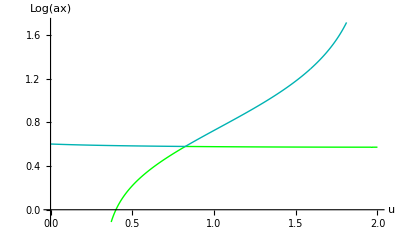

```mathematica
Clear[uinf,myuinf,λ];
mylambda=mylambdamin;(* mylambdamin;*)(*lambdaminrealnum;*)
myquart=quarticstarnum//.{λ->mylambda};

(* for a given λ, find such uinf that at the star u = u0 *)

mymusol=Solve[0==quarticstarnummu//.{λ->mylambda,σ->mysigma},{μ}]
mymu= mymusol[[Length[mymusol],1,2]];

myuinfsol=Solve[(√(1+uinf^2) (uinf+σ))/uinf==mymu,{uinf}]//.{σ->mysigma}
myuinf=myuinfsol[[Length[myuinfsol],1,2]];

Print["u0=",myu0,"     ucr= ",(μ-λ σ)/λ//.{μ->mymu,λ->mylambda,σ->mysigma,uinf->myuinf},"    uinf=",myuinf,"  lambda=",mylambda, "  mu=", mymu];

myquart=quarticstarnumallx//.{λ->mylambda}
mysolve=Solve[myquart==0,x];
soll=mysolve;

fun1=mya*x/.(soll[[1]]);
fun2=mya*x/.(soll[[2]]);
fun3=mya*x/.(soll[[3]]);
fun4=mya*x/.(soll[[4]]);
nfun1=If[Abs[Im[fun1]]<10^(-5),Re[fun1],10^(-10)*I];
nfun2=If[Abs[Im[fun2]]<10^(-5),Re[fun2],10^(-10)*I];
nfun3=If[Abs[Im[fun3]]<10^(-5),Re[fun3],10^(-10)*I];
nfun4=If[Abs[Im[fun4]]<10^(-5),Re[fun4],10^(-10)*I];
nnfun1=Log[10,Abs[nfun1]]+UnitStep[-nfun1] I;
nnfun2=Log[10,Abs[nfun2]]+UnitStep[-nfun2] I;
nnfun3=Log[10,Abs[nfun3]]+UnitStep[-nfun3] I;
nnfun4=Log[10,Abs[nfun4]]+UnitStep[-nfun4] I;
(*mypl=Plot[{-Log[10,-Re[mya x/.(soll[[1]])]],Log[10,Re[mya x/.(soll[[2]])]],-Log[10,Re[-mya x/.(soll[[3]])]],Log[10,Re[mya x/.(soll[[4]])]]},{u,myu0,myuinf*5},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]}]*)
(*mypl=Plot[{nnfun1,nnfun2,nnfun3,nnfun4},{u,myuinf*0.9,myu0*10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->1000]*)

(*mypl=Plot[{nnfun1,nnfun2,nnfun3,nnfun4},{u,Min[myu0,myuinf]0.0001,1.1Max[myu0,myuinf]},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->1000,AxesLabel->{u,"Log(ax)"}]*)

mypl=Plot[{nnfun1,nnfun2,nnfun3,nnfun4},{u,myu0 0.0000001,5myu0},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->10000,AxesLabel->{u,"Log(ax)"}]


(*mypl=Plot[{nnfun1,nnfun2,nnfun3,nnfun4},{u,15.5,16},
PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->1000,AxesLabel->{u,"Log(ax)"}]*)

(*mypl=Plot[{nnfun1,nnfun2,nnfun3,nnfun4},{u,myuinf*0.9,myuinf*10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->100]*)
```

```mathematica
myuinfsol
```

myuinfsol

```mathematica
fun4/.u->(0.9999999)mysigma^(1/3)
```

7.09588×10^7

```mathematica
(* rows=which uinf, columns=which root for x(u) *)
matrixcol={fun1,fun2,fun3,fun4};
matrixx=Table[matrixcol[[j]],{i,1,Length[myuinfsol]},{j,1,4}];
matrixxatuinf=Table[matrixx[[i,j]]//.{u->0.999999uinf}//.myuinfsol[[i]],{i,1,Length[myuinfsol]},{j,1,4}]
MatrixForm[matrixxatuinf]
```

{{-1.16197×10^-16-1.89763 ⅈ,1.16197×10^-16+1.89763 ⅈ,-3230.02-3.59886×10^-16 ⅈ,3230.02+3.59886×10^-16 ⅈ},{-2.95603+4.9354×10^-22 ⅈ,2.95603-4.9354×10^-22 ⅈ,-2929.06+3.87867×10^-13 ⅈ,2929.06-3.87867×10^-13 ⅈ},{-3.74044-3.77278×10^-9 ⅈ,3.74044+3.77278×10^-9 ⅈ,-4.26739×10^6+34.9955 ⅈ,4.26739×10^6-34.9955 ⅈ},{-3.74069+0. ⅈ,3.74069+0. ⅈ,-4.26767×10^6-35.0018 ⅈ,4.26767×10^6+35.0018 ⅈ}}

(-1.16197×10^-16-1.89763 ⅈ | 1.16197×10^-16+1.89763 ⅈ | -3230.02-3.59886×10^-16 ⅈ | 3230.02+3.59886×10^-16 ⅈ
-2.95603+4.9354×10^-22 ⅈ | 2.95603-4.9354×10^-22 ⅈ | -2929.06+3.87867×10^-13 ⅈ | 2929.06-3.87867×10^-13 ⅈ
-3.74044-3.77278×10^-9 ⅈ | 3.74044+3.77278×10^-9 ⅈ | -4.26739×10^6+34.9955 ⅈ | 4.26739×10^6-34.9955 ⅈ
-3.74069+0. ⅈ | 3.74069+0. ⅈ | -4.26767×10^6-35.0018 ⅈ | 4.26767×10^6+35.0018 ⅈ)

```mathematica
soln[[1]]
```

{uinf→-18.266}

```mathematica
soll//.{u->1.9640454829551424}
```

{{x→0.-4.70189×10^6 ⅈ},{x→0.+4.70189×10^6 ⅈ},{x→-0.336573},{x→0.336573}}

```mathematica
fun4//.{u->-18.265967708506086}
```

9.63411×10^7

```mathematica
Clear[uinf,myuinf,λ];
mylambda=1.25;
myquart=quarticstarnum//.{λ->mylambda};

(* for a given λ, find such uinf that at the star u = u0 *)
soln=Solve[myquart==0,{uinf}]
myuinf=soln[[6,1,2]];
uinffun[myl_]:=((uinf//.Solve[(quarticstarnum/.λ->myl)==0,{uinf}])[[3]]);
Print["uinf=",myuinf,"  lambda=",mylambda];
myquart=quarticstarnumallx//.{λ->mylambda}//.{uinf->myuinf};
(*ImplicitPlot[myquart==0,{x,1/mya,10^2},{u,myu0/10^(10),myuinf*5},PlotPoints->200]*)
mysolve=Solve[myquart==0,x];
(*Plot[Re[mysolve[[2,1,2]]],{u,myu0/10^10,0.2}]*)
mymu//.{uinf->myuinf,σ->mysigma}


soll=mysolve;
fun1=mya*x/.(soll[[1]]);
fun2=mya*x/.(soll[[2]]);
fun3=mya*x/.(soll[[3]]);
fun4=mya*x/.(soll[[4]]);
nfun1=If[Abs[Im[fun1]]<10^(-12),Re[fun1],10^(-10)*I];
nfun2=If[Abs[Im[fun2]]<10^(-12),Re[fun2],10^(-10)*I];
nfun3=If[Abs[Im[fun3]]<10^(-12),Re[fun3],10^(-10)*I];
nfun4=If[Abs[Im[fun4]]<10^(-12),Re[fun4],10^(-10)*I];
nnfun1=Log[10,Abs[nfun1]]+UnitStep[-nfun1] I;
nnfun2=Log[10,Abs[nfun2]]+UnitStep[-nfun2] I;
nnfun3=Log[10,Abs[nfun3]]+UnitStep[-nfun3] I;
nnfun4=Log[10,Abs[nfun4]]+UnitStep[-nfun4] I;
(*mypl=Plot[{-Log[10,-Re[mya x/.(soll[[1]])]],Log[10,Re[mya x/.(soll[[2]])]],-Log[10,Re[-mya x/.(soll[[3]])]],Log[10,Re[mya x/.(soll[[4]])]]},{u,myu0,myuinf*5},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]}]*)
(*mypl=Plot[{nnfun1,nnfun2,nnfun3,nnfun4},{u,myuinf*0.9,myu0*10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->1000]*)

mypl=Plot[{nnfun1,nnfun2,nnfun3,nnfun4},{u,myu0/10^10,myu0*10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->1000]

(*mypl=Plot[{nnfun1,nnfun2,nnfun3,nnfun4},{u,myuinf*0.9,myuinf*10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.,0.7,0.7]},PlotPoints->100]*)
```

{{uinf→-18.1751},{uinf→-15.8851},{uinf→0.963253-1.44867 ⅈ},{uinf→0.963253+1.44867 ⅈ},{uinf→1.92346-0.36253 ⅈ},{uinf→1.92346+0.36253 ⅈ}}

uinf=1.92346+0.36253 ⅈ  lambda=1.25

10.6149+0. ⅈ

Plot::plnr: nnfun1 is not a machine-size real number at u = 6.06601×10^-9. More…

Plot::plnr: nnfun1 is not a machine-size real number at u = 0.00584749. More…

Plot::plnr: nnfun1 is not a machine-size real number at u = 0.0122247. More…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. More…

⁃Graphics⁃

```mathematica
Solve[fun2==fun4,{u}]
```

$Aborted

```mathematica
mysolve//.u->myu0
fun2//.u->51
fun4//.u->51
myu0
1/mya
```

{{x→-0.0908265},{x→0.0908265},{x→-0.131784},{x→0.131784}}

1.44522

1.53251

50

0.0908265

```mathematica
sols//.{μ->mymu,λ->mylambda,uinf->myuinf,σ->mysigma}
```

General::spell: Possible spelling error: new symbol name "sols" is similar to existing symbols {soll, soln}. More…

sols

```mathematica
x//.soll//.u->40
(1+u^2)(u+σ)^2-μ^2 u^2//.u->40//.μ->mymu//.uinf->myuinf//.σ->mysigma
```

{-0.124757,0.124757,-0.152355,0.152355}

-5.09446×10^6

```mathematica
sols=Solve[0==quarticallx,x];
```

General::spell1: Possible spelling error: new symbol name "sols" is similar to existing symbol "soll". More…

```mathematica
quarticallx
```

1+u^2-(-λ σ+(√(1+uinf^2) (uinf+σ))/uinf)^2+x^4 ((1+u^2) (u+σ)^2-(u^2 (1+uinf^2) (uinf+σ)^2)/uinf^2)+x^2 (-2 (1+u^2) (u+σ)+(2 u √(1+uinf^2) (uinf+σ) (-λ σ+(√(1+uinf^2) (uinf+σ))/uinf))/uinf+σ (-λ (u+σ)+(√(1+uinf^2) (uinf+σ))/uinf)^2)

```mathematica
myusols=Solve[0==(-4 (u^4 uinf^2-u^2 uinf^4-2 u^2 uinf σ+2 u uinf^2 σ+2 u^3 uinf^2 σ-2 u^2 uinf^3 σ-u^2 σ^2+uinf^2 σ^2) (u^2 uinf^2-uinf^4-2 uinf σ-2 uinf^3 σ+2 uinf^2 √(1+uinf^2) λ σ-σ^2-uinf^2 σ^2+2 uinf √(1+uinf^2) λ σ^2-uinf^2 λ^2 σ^2)+(-2 u^3 uinf^2+2 u uinf^4+4 u uinf σ-uinf^2 σ-2 u^2 uinf^2 σ+4 u uinf^3 σ+uinf^4 σ-4 u uinf^2 √(1+uinf^2) λ σ+u^2 uinf^2 λ^2 σ+2 u σ^2+2 uinf σ^2+2 u uinf^2 σ^2+2 uinf^3 σ^2-4 u uinf √(1+uinf^2) λ σ^2-2 uinf^2 √(1+uinf^2) λ σ^2+2 u uinf^2 λ^2 σ^2+σ^3+uinf^2 σ^3-2 uinf √(1+uinf^2) λ σ^3+uinf^2 λ^2 σ^3)^2),u];
```

```mathematica
myusols//.{σ->mysigma,Ω->myomega}
```

{{u→Root[-24961.6-13178.9 uinf-52532.5 uinf^2-26587.4 uinf^3-30187.7 uinf^4-13638.1 uinf^5-2624.4 uinf^6-229.599 uinf^7-7.57626 uinf^8+99846.6 uinf √(1+uinf^2) λ+39536.6 uinf^2 √(1+uinf^2) λ+105065. uinf^3 √(1+uinf^2) λ+39766.2 uinf^4 √(1+uinf^2) λ+5218.49 uinf^5 √(1+uinf^2) λ+229.599 uinf^6 √(1+uinf^2) λ-149770. uinf^2 λ^2-39536.6 uinf^3 λ^2-152379. uinf^4 λ^2-39536.6 uinf^5 λ^2-2609.25 uinf^6 λ^2+99846.6 uinf^3 √(1+uinf^2) λ^3+13178.9 uinf^4 √(1+uinf^2) λ^3-24961.6 uinf^4 λ^4+(-13178.9-6957.99 uinf-27505.8 uinf^2-13976.6 uinf^3-15704.5 uinf^4-7139.82 uinf^5-1381.59 uinf^6-121.22 uinf^7-4 uinf^8+52715.5 uinf √(1+uinf^2) λ+20874. uinf^2 √(1+uinf^2) λ+55011.5 uinf^3 √(1+uinf^2) λ+20934.6 uinf^4 √(1+uinf^2) λ+2755.18 uinf^5 √(1+uinf^2) λ+121.22 uinf^6 √(1+uinf^2) λ-79073.3 uinf^2 λ^2-20874. uinf^3 λ^2-80221.3 uinf^4 λ^2-20874. uinf^5 λ^2-1377.59 uinf^6 λ^2+52715.5 uinf^3 √(1+uinf^2) λ^3+6957.99 uinf^4 √(1+uinf^2) λ^3-13178.9 uinf^4 λ^4) #1+(3479. uinf √(1+uinf^2) λ+1377.59 uinf^2 √(1+uinf^2) λ+3600.22 uinf^3 √(1+uinf^2) λ+1377.59 uinf^4 √(1+uinf^2) λ+181.83 uinf^5 √(1+uinf^2) λ+8 uinf^6 √(1+uinf^2) λ-9567.24 uinf^2 λ^2-2525.58 uinf^3 λ^2-9673.31 uinf^4 λ^2-2525.58 uinf^5 λ^2-166.678 uinf^6 λ^2+8697.49 uinf^3 √(1+uinf^2) λ^3+1147.99 uinf^4 √(1+uinf^2) λ^3-2609.25 uinf^4 λ^4) #1^2+(229.599 uinf^2+60.6101 uinf^3+233.599 uinf^4+60.6101 uinf^5+4 uinf^6-459.197 uinf^3 √(1+uinf^2) λ-60.6101 uinf^4 √(1+uinf^2) λ-229.599 uinf^2 λ^2-60.6101 uinf^3 λ^2-60.6101 uinf^5 λ^2-4 uinf^6 λ^2+459.197 uinf^3 √(1+uinf^2) λ^3+60.6101 uinf^4 √(1+uinf^2) λ^3-229.599 uinf^4 λ^4) #1^3+(-60.6101 uinf^3 √(1+uinf^2) λ-8 uinf^4 √(1+uinf^2) λ+60.6101 uinf^4 λ^2-7.57626 uinf^4 λ^4) #1^4+4 uinf^4 λ^2 #1^5&,1]},{u→Root[-24961.6-13178.9 uinf-52532.5 uinf^2-26587.4 uinf^3-30187.7 uinf^4-13638.1 uinf^5-2624.4 uinf^6-229.599 uinf^7-7.57626 uinf^8+99846.6 uinf √(1+uinf^2) λ+39536.6 uinf^2 √(1+uinf^2) λ+105065. uinf^3 √(1+uinf^2) λ+39766.2 uinf^4 √(1+uinf^2) λ+5218.49 uinf^5 √(1+uinf^2) λ+229.599 uinf^6 √(1+uinf^2) λ-149770. uinf^2 λ^2-39536.6 uinf^3 λ^2-152379. uinf^4 λ^2-39536.6 uinf^5 λ^2-2609.25 uinf^6 λ^2+99846.6 uinf^3 √(1+uinf^2) λ^3+13178.9 uinf^4 √(1+uinf^2) λ^3-24961.6 uinf^4 λ^4+(-13178.9-6957.99 uinf-27505.8 uinf^2-13976.6 uinf^3-15704.5 uinf^4-7139.82 uinf^5-1381.59 uinf^6-121.22 uinf^7-4 uinf^8+52715.5 uinf √(1+uinf^2) λ+20874. uinf^2 √(1+uinf^2) λ+55011.5 uinf^3 √(1+uinf^2) λ+20934.6 uinf^4 √(1+uinf^2) λ+2755.18 uinf^5 √(1+uinf^2) λ+121.22 uinf^6 √(1+uinf^2) λ-79073.3 uinf^2 λ^2-20874. uinf^3 λ^2-80221.3 uinf^4 λ^2-20874. uinf^5 λ^2-1377.59 uinf^6 λ^2+52715.5 uinf^3 √(1+uinf^2) λ^3+6957.99 uinf^4 √(1+uinf^2) λ^3-13178.9 uinf^4 λ^4) #1+(3479. uinf √(1+uinf^2) λ+1377.59 uinf^2 √(1+uinf^2) λ+3600.22 uinf^3 √(1+uinf^2) λ+1377.59 uinf^4 √(1+uinf^2) λ+181.83 uinf^5 √(1+uinf^2) λ+8 uinf^6 √(1+uinf^2) λ-9567.24 uinf^2 λ^2-2525.58 uinf^3 λ^2-9673.31 uinf^4 λ^2-2525.58 uinf^5 λ^2-166.678 uinf^6 λ^2+8697.49 uinf^3 √(1+uinf^2) λ^3+1147.99 uinf^4 √(1+uinf^2) λ^3-2609.25 uinf^4 λ^4) #1^2+(229.599 uinf^2+60.6101 uinf^3+233.599 uinf^4+60.6101 uinf^5+4 uinf^6-459.197 uinf^3 √(1+uinf^2) λ-60.6101 uinf^4 √(1+uinf^2) λ-229.599 uinf^2 λ^2-60.6101 uinf^3 λ^2-60.6101 uinf^5 λ^2-4 uinf^6 λ^2+459.197 uinf^3 √(1+uinf^2) λ^3+60.6101 uinf^4 √(1+uinf^2) λ^3-229.599 uinf^4 λ^4) #1^3+(-60.6101 uinf^3 √(1+uinf^2) λ-8 uinf^4 √(1+uinf^2) λ+60.6101 uinf^4 λ^2-7.57626 uinf^4 λ^4) #1^4+4 uinf^4 λ^2 #1^5&,2]},{u→Root[-24961.6-13178.9 uinf-52532.5 uinf^2-26587.4 uinf^3-30187.7 uinf^4-13638.1 uinf^5-2624.4 uinf^6-229.599 uinf^7-7.57626 uinf^8+99846.6 uinf √(1+uinf^2) λ+39536.6 uinf^2 √(1+uinf^2) λ+105065. uinf^3 √(1+uinf^2) λ+39766.2 uinf^4 √(1+uinf^2) λ+5218.49 uinf^5 √(1+uinf^2) λ+229.599 uinf^6 √(1+uinf^2) λ-149770. uinf^2 λ^2-39536.6 uinf^3 λ^2-152379. uinf^4 λ^2-39536.6 uinf^5 λ^2-2609.25 uinf^6 λ^2+99846.6 uinf^3 √(1+uinf^2) λ^3+13178.9 uinf^4 √(1+uinf^2) λ^3-24961.6 uinf^4 λ^4+(-13178.9-6957.99 uinf-27505.8 uinf^2-13976.6 uinf^3-15704.5 uinf^4-7139.82 uinf^5-1381.59 uinf^6-121.22 uinf^7-4 uinf^8+52715.5 uinf √(1+uinf^2) λ+20874. uinf^2 √(1+uinf^2) λ+55011.5 uinf^3 √(1+uinf^2) λ+20934.6 uinf^4 √(1+uinf^2) λ+2755.18 uinf^5 √(1+uinf^2) λ+121.22 uinf^6 √(1+uinf^2) λ-79073.3 uinf^2 λ^2-20874. uinf^3 λ^2-80221.3 uinf^4 λ^2-20874. uinf^5 λ^2-1377.59 uinf^6 λ^2+52715.5 uinf^3 √(1+uinf^2) λ^3+6957.99 uinf^4 √(1+uinf^2) λ^3-13178.9 uinf^4 λ^4) #1+(3479. uinf √(1+uinf^2) λ+1377.59 uinf^2 √(1+uinf^2) λ+3600.22 uinf^3 √(1+uinf^2) λ+1377.59 uinf^4 √(1+uinf^2) λ+181.83 uinf^5 √(1+uinf^2) λ+8 uinf^6 √(1+uinf^2) λ-9567.24 uinf^2 λ^2-2525.58 uinf^3 λ^2-9673.31 uinf^4 λ^2-2525.58 uinf^5 λ^2-166.678 uinf^6 λ^2+8697.49 uinf^3 √(1+uinf^2) λ^3+1147.99 uinf^4 √(1+uinf^2) λ^3-2609.25 uinf^4 λ^4) #1^2+(229.599 uinf^2+60.6101 uinf^3+233.599 uinf^4+60.6101 uinf^5+4 uinf^6-459.197 uinf^3 √(1+uinf^2) λ-60.6101 uinf^4 √(1+uinf^2) λ-229.599 uinf^2 λ^2-60.6101 uinf^3 λ^2-60.6101 uinf^5 λ^2-4 uinf^6 λ^2+459.197 uinf^3 √(1+uinf^2) λ^3+60.6101 uinf^4 √(1+uinf^2) λ^3-229.599 uinf^4 λ^4) #1^3+(-60.6101 uinf^3 √(1+uinf^2) λ-8 uinf^4 √(1+uinf^2) λ+60.6101 uinf^4 λ^2-7.57626 uinf^4 λ^4) #1^4+4 uinf^4 λ^2 #1^5&,3]},{u→Root[-24961.6-13178.9 uinf-52532.5 uinf^2-26587.4 uinf^3-30187.7 uinf^4-13638.1 uinf^5-2624.4 uinf^6-229.599 uinf^7-7.57626 uinf^8+99846.6 uinf √(1+uinf^2) λ+39536.6 uinf^2 √(1+uinf^2) λ+105065. uinf^3 √(1+uinf^2) λ+39766.2 uinf^4 √(1+uinf^2) λ+5218.49 uinf^5 √(1+uinf^2) λ+229.599 uinf^6 √(1+uinf^2) λ-149770. uinf^2 λ^2-39536.6 uinf^3 λ^2-152379. uinf^4 λ^2-39536.6 uinf^5 λ^2-2609.25 uinf^6 λ^2+99846.6 uinf^3 √(1+uinf^2) λ^3+13178.9 uinf^4 √(1+uinf^2) λ^3-24961.6 uinf^4 λ^4+(-13178.9-6957.99 uinf-27505.8 uinf^2-13976.6 uinf^3-15704.5 uinf^4-7139.82 uinf^5-1381.59 uinf^6-121.22 uinf^7-4 uinf^8+52715.5 uinf √(1+uinf^2) λ+20874. uinf^2 √(1+uinf^2) λ+55011.5 uinf^3 √(1+uinf^2) λ+20934.6 uinf^4 √(1+uinf^2) λ+2755.18 uinf^5 √(1+uinf^2) λ+121.22 uinf^6 √(1+uinf^2) λ-79073.3 uinf^2 λ^2-20874. uinf^3 λ^2-80221.3 uinf^4 λ^2-20874. uinf^5 λ^2-1377.59 uinf^6 λ^2+52715.5 uinf^3 √(1+uinf^2) λ^3+6957.99 uinf^4 √(1+uinf^2) λ^3-13178.9 uinf^4 λ^4) #1+(3479. uinf √(1+uinf^2) λ+1377.59 uinf^2 √(1+uinf^2) λ+3600.22 uinf^3 √(1+uinf^2) λ+1377.59 uinf^4 √(1+uinf^2) λ+181.83 uinf^5 √(1+uinf^2) λ+8 uinf^6 √(1+uinf^2) λ-9567.24 uinf^2 λ^2-2525.58 uinf^3 λ^2-9673.31 uinf^4 λ^2-2525.58 uinf^5 λ^2-166.678 uinf^6 λ^2+8697.49 uinf^3 √(1+uinf^2) λ^3+1147.99 uinf^4 √(1+uinf^2) λ^3-2609.25 uinf^4 λ^4) #1^2+(229.599 uinf^2+60.6101 uinf^3+233.599 uinf^4+60.6101 uinf^5+4 uinf^6-459.197 uinf^3 √(1+uinf^2) λ-60.6101 uinf^4 √(1+uinf^2) λ-229.599 uinf^2 λ^2-60.6101 uinf^3 λ^2-60.6101 uinf^5 λ^2-4 uinf^6 λ^2+459.197 uinf^3 √(1+uinf^2) λ^3+60.6101 uinf^4 √(1+uinf^2) λ^3-229.599 uinf^4 λ^4) #1^3+(-60.6101 uinf^3 √(1+uinf^2) λ-8 uinf^4 √(1+uinf^2) λ+60.6101 uinf^4 λ^2-7.57626 uinf^4 λ^4) #1^4+4 uinf^4 λ^2 #1^5&,4]},{u→Root[-24961.6-13178.9 uinf-52532.5 uinf^2-26587.4 uinf^3-30187.7 uinf^4-13638.1 uinf^5-2624.4 uinf^6-229.599 uinf^7-7.57626 uinf^8+99846.6 uinf √(1+uinf^2) λ+39536.6 uinf^2 √(1+uinf^2) λ+105065. uinf^3 √(1+uinf^2) λ+39766.2 uinf^4 √(1+uinf^2) λ+5218.49 uinf^5 √(1+uinf^2) λ+229.599 uinf^6 √(1+uinf^2) λ-149770. uinf^2 λ^2-39536.6 uinf^3 λ^2-152379. uinf^4 λ^2-39536.6 uinf^5 λ^2-2609.25 uinf^6 λ^2+99846.6 uinf^3 √(1+uinf^2) λ^3+13178.9 uinf^4 √(1+uinf^2) λ^3-24961.6 uinf^4 λ^4+(-13178.9-6957.99 uinf-27505.8 uinf^2-13976.6 uinf^3-15704.5 uinf^4-7139.82 uinf^5-1381.59 uinf^6-121.22 uinf^7-4 uinf^8+52715.5 uinf √(1+uinf^2) λ+20874. uinf^2 √(1+uinf^2) λ+55011.5 uinf^3 √(1+uinf^2) λ+20934.6 uinf^4 √(1+uinf^2) λ+2755.18 uinf^5 √(1+uinf^2) λ+121.22 uinf^6 √(1+uinf^2) λ-79073.3 uinf^2 λ^2-20874. uinf^3 λ^2-80221.3 uinf^4 λ^2-20874. uinf^5 λ^2-1377.59 uinf^6 λ^2+52715.5 uinf^3 √(1+uinf^2) λ^3+6957.99 uinf^4 √(1+uinf^2) λ^3-13178.9 uinf^4 λ^4) #1+(3479. uinf √(1+uinf^2) λ+1377.59 uinf^2 √(1+uinf^2) λ+3600.22 uinf^3 √(1+uinf^2) λ+1377.59 uinf^4 √(1+uinf^2) λ+181.83 uinf^5 √(1+uinf^2) λ+8 uinf^6 √(1+uinf^2) λ-9567.24 uinf^2 λ^2-2525.58 uinf^3 λ^2-9673.31 uinf^4 λ^2-2525.58 uinf^5 λ^2-166.678 uinf^6 λ^2+8697.49 uinf^3 √(1+uinf^2) λ^3+1147.99 uinf^4 √(1+uinf^2) λ^3-2609.25 uinf^4 λ^4) #1^2+(229.599 uinf^2+60.6101 uinf^3+233.599 uinf^4+60.6101 uinf^5+4 uinf^6-459.197 uinf^3 √(1+uinf^2) λ-60.6101 uinf^4 √(1+uinf^2) λ-229.599 uinf^2 λ^2-60.6101 uinf^3 λ^2-60.6101 uinf^5 λ^2-4 uinf^6 λ^2+459.197 uinf^3 √(1+uinf^2) λ^3+60.6101 uinf^4 √(1+uinf^2) λ^3-229.599 uinf^4 λ^4) #1^3+(-60.6101 uinf^3 √(1+uinf^2) λ-8 uinf^4 √(1+uinf^2) λ+60.6101 uinf^4 λ^2-7.57626 uinf^4 λ^4) #1^4+4 uinf^4 λ^2 #1^5&,5]}}

```mathematica
(* check if roots match *)
myquart=quarticstarnumallx//.{uinf->myuinf}
solquart=Solve[0==myquart,x]//.u->49.89//.λ->mylambda
```

1+u^2+(-3316.05 u^2+(7.57626+u)^2 (1+u^2)) x^4-(57.5852-7.57626 λ)^2+x^2 (-2 (7.57626+u) (1+u^2)+115.17 u (57.5852-7.57626 λ)+7.57626 (57.5852-(7.57626+u) λ)^2)

{{x→-0.131847},{x→0.131847},{x→-0.142661},{x→0.142661}}

```mathematica
FindRoot[solquart[[2,1,2]]==solquart[[4,1,2]]
```

{{x→0.-5.25811×10^7 ⅈ},{x→0.+5.25811×10^7 ⅈ},{x→0.},{x→0.}}

```mathematica
FindRoot[soll[[2,1,2]]==soll[[4,1,2]],{u,myu0}]
```

{u→50.4987+0. ⅈ}

```mathematica
fun1+fun2
```

0. √(-(2. (17769.3+4692.78 u-13.2584 u^2-2. u^3))/(57.3997+15.1525 u-2670.41 u^2+15.1525 u^3+u^4)-2. √(((17769.3+4692.78 u-13.2584 u^2-2. u^3)^2)/((57.3997+15.1525 u-2670.41 u^2+15.1525 u^3+u^4)^2)-(4. (-2346.39+u^2))/(57.3997+15.1525 u-2670.41 u^2+15.1525 u^3+u^4)))

```mathematica
Rl=1/myomega
```

4.

```mathematica
ucr=(mymu/mylambda-mysigma)//.{uinf->myuinf,σ->mysigma}
```

Power::infy: Infinite expression 1/0 encountered. More…

ComplexInfinity

```mathematica
mysolve//.{u->myuinf}
```

{{x→0.},{x→0.},{x→-8.99897×10^8},{x→8.99897×10^8}}

```mathematica
Solve[0==myquart//.{x->10^8},u]
```

{{u→-56.9525},{u→-0.152065},{u→0.158584},{u→41.7934}}

```mathematica
myuinf
```

0.158584

```mathematica
fun1//.{u->45}
```

0.-2.46449 ⅈ

```mathematica
myu0
```

50

```mathematica
mysolve[[2,1,2]]
```

0.5 √(-(2. (18461.5+4875.53 u-15.1525 u^2-2. u^3))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)-2. √(((18461.5+4875.53 u-15.1525 u^2-2. u^3)^2)/((57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)^2)-(4. (-2437.76+u^2))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)))

```mathematica
Re[x/.mysolve]/.u->1.3333333125 10^-8
```

{0.,0.,-0.363306,0.363306}

```mathematica
mysolve
```

{{x→-0.5 √(-(2. (18461.5+4875.53 u-15.1525 u^2-2. u^3))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)-2. √(((18461.5+4875.53 u-15.1525 u^2-2. u^3)^2)/((57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)^2)-(4. (-2437.76+u^2))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)))},{x→0.5 √(-(2. (18461.5+4875.53 u-15.1525 u^2-2. u^3))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)-2. √(((18461.5+4875.53 u-15.1525 u^2-2. u^3)^2)/((57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)^2)-(4. (-2437.76+u^2))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)))},{x→-0.5 √(-(2. (18461.5+4875.53 u-15.1525 u^2-2. u^3))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)+2. √(((18461.5+4875.53 u-15.1525 u^2-2. u^3)^2)/((57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)^2)-(4. (-2437.76+u^2))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)))},{x→0.5 √(-(2. (18461.5+4875.53 u-15.1525 u^2-2. u^3))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)+2. √(((18461.5+4875.53 u-15.1525 u^2-2. u^3)^2)/((57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)^2)-(4. (-2437.76+u^2))/(57.3997+15.1525 u-2380.36 u^2+15.1525 u^3+u^4)))}}

```mathematica
myquart
```

-2437.76+u^2+(18476.7+4877.53 u-2 (7.57626+u) (1+u^2)) x^2+(-2438.76 u^2+(7.57626+u)^2 (1+u^2)) x^4

```mathematica
Block[{λmin=-3;
λmax=3;
cont = 1;
λ=λmin;},

uinfsol=FindRoot[==0,{uinf,myu0}]; 
mylen = Length[MessageList[-1]];
If[mylen==0,Print["Bad λmin", uinfsol]];

λ=λmax;
uinfsol=FindRoot[quarticstarnum==0,{uinf,myu0}]; 
mylen = Length[MessageList[-1]];
If[mylen!=0,Print["Bad λmax" , uinfsol]];


For[i=0,i<maxi && Abs[λmax-λmin]<10^-5,i++,
λ=(λmax+λmin)/2;
FindRoot[quarticstarnum==0,{uinf,myu0}]; 
mylen = Length[MessageList[-1]];
If[mylen==0,λmax=λ,λmin=λ];
];
solλ=λ;
Print[solλ];
]
```

Syntax::sntxf: "FindRoot[" cannot be followed by "== 0, {uinf, myu0}]"."" More…

Block[{λmin=-3;λmax=3;cont=1;λ=λmin;},uinfsol=FindRoot[==,{uinf,myu0}];mylen=Length[MessageList[-1]];If[mylen==0,Print["Bad λmin",uinfsol]];λ=λmax;uinfsol=FindRoot[quarticstarnum==0,{uinf,myu0}];mylen=Length[MessageList[-1]];If[mylen!=0,Print["Bad λmax",uinfsol]];For[i=0,i<maxi&&Abs[λmax-λmin]<10^-5,i++,λ=(λmax+λmin)/2;FindRoot[quarticstarnum==0,{uinf,myu0}];mylen=Length[MessageList[-1]];If[mylen==0,λmax=λ,λmin=λ];];solλ=λ;Print[solλ];]

```mathematica
{1.24781,2.004}
```

{1.24781,2.004}

```mathematica
mysigma^(1/3)
```

1.96405

```mathematica
fun1real=A1
```

-u^2 μ^2+(1+u^2) (u+σ)^2

```mathematica
(*fun1=u^4+D3*u^3+D2*u^2+D1*u+D0*)
fun1=fun1real
fun2=(u-eta)^2
remain=PolynomialRemainder[fun1,fun2,u]
```

-u^2 μ^2+(1+u^2) (u+σ)^2

(-eta+u)^2

-eta^2-3 eta^4+eta^2 μ^2-4 eta^3 σ+σ^2-eta^2 σ^2+u (2 eta+4 eta^3-2 eta μ^2+2 σ+6 eta^2 σ+2 eta σ^2)

```mathematica
part1=remain//.{u->0}
part2=(remain-part1)/u
```

-eta^2-3 eta^4+eta^2 μ^2-4 eta^3 σ+σ^2-eta^2 σ^2

2 eta+4 eta^3-2 eta μ^2+2 σ+6 eta^2 σ+2 eta σ^2

```mathematica
Solve[{part1==0,part2==0},{eta,μ}]
```

{{μ→0,eta→-σ},{μ→0,eta→-σ},{μ→-(√(σ+3 σ^(5/3)+3 σ^(7/3)+σ^3))/(√σ),eta→σ^(1/3)},{μ→(√(σ+3 σ^(5/3)+3 σ^(7/3)+σ^3))/(√σ),eta→σ^(1/3)},{μ→-(√(σ+3 (-1)^(2/3) σ^(5/3)-3 (-1)^(1/3) σ^(7/3)+σ^3))/(√σ),eta→-(-1)^(1/3) σ^(1/3)},{μ→(√(σ+3 (-1)^(2/3) σ^(5/3)-3 (-1)^(1/3) σ^(7/3)+σ^3))/(√σ),eta→-(-1)^(1/3) σ^(1/3)},{μ→-(√(σ-3 (-1)^(1/3) σ^(5/3)+3 (-1)^(2/3) σ^(7/3)+σ^3))/(√σ),eta→(-1)^(2/3) σ^(1/3)},{μ→(√(σ-3 (-1)^(1/3) σ^(5/3)+3 (-1)^(2/3) σ^(7/3)+σ^3))/(√σ),eta→(-1)^(2/3) σ^(1/3)}}

```mathematica
K=3*eta^2+2*D3*eta+D2
part1mich=Expand[D0-eta^2*K]
part2mich=Expand[2*eta*K+D1-eta^2*(D3+2*eta)]
```

D2+2 D3 eta+3 eta^2

D0-D2 eta^2-2 D3 eta^3-3 eta^4

D1+2 D2 eta+3 D3 eta^2+4 eta^3

```mathematica
FindRoot
```

FindRoot